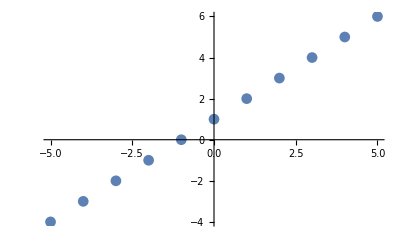

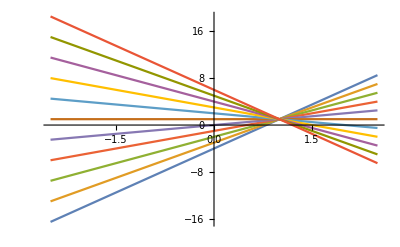

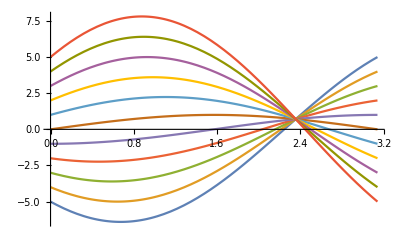

```mathematica
Data=Table[{x,x+1},{x,-5,5}];

Show[ListPlot[Data,PlotMarkers->{Automatic,11},Joined->False]]

pSIF[m_,x_,y_]:=-x*m+y
pNF[t_,x_,y_]:=x*Cos[t]+y*Sin[t]

Show[Plot[Apply[pSIF[m,#1,#2]&,Data,{1}],{m,-2.5,2.5},Evaluated->True,PlotRange->{Automatic,Automatic}]]
Show[Plot[Apply[pNF[m,#1,#2]&,Data,{1}],{m,0,Pi},Evaluated->True,PlotRange->{{0,Pi},Automatic}]]
```

```mathematica
data=Table[{x,x+1},{x,-5,5}]
```

{{-5,-4},{-4,-3},{-3,-2},{-2,-1},{-1,0},{0,1},{1,2},{2,3},{3,4},{4,5},{5,6}}

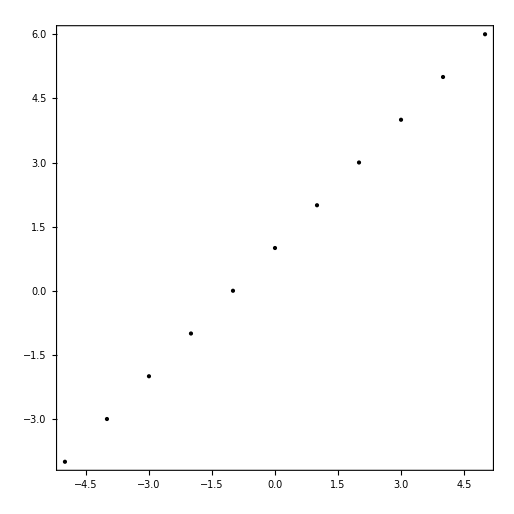

```mathematica
Graphics[Point[data],Axes->True,Frame->True]
```

```mathematica
pSIF[m_,x_,y_]:=-x*m+y
```

```mathematica
pNF[t_,x_,y_]:=x*Cos[t]+y*Sin[t]
```

```mathematica
pSIF[-2.5,x,y]
```

2.5 x+y

```mathematica
data2=Flatten[Table[{m,#}&/@Apply[pNF[m,#1,#2]&,Data,{1}],{m,0,Pi,0.1}],1]
```

{{0.,-5.},{0.,-4.},{0.,-3.},{0.,-2.},{0.,-1.},{0.,0.},{0.,1.},{0.,2.},{0.,3.},{0.,4.},{0.,5.},{0.1,-5.37435},{0.1,-4.27952},{0.1,-3.18468},{0.1,-2.08984},{0.1,-0.995004},{0.1,0.0998334},{0.1,1.19467},{0.1,2.28951},{0.1,3.38435},{0.1,4.47918},{0.1,5.57402},{0.2,-5.69501},{0.2,-4.51627},{0.2,-3.33754},{0.2,-2.1588},{0.2,-0.980067},{0.2,0.198669},{0.2,1.37741},{0.2,2.55614},{0.2,3.73488},{0.2,4.91361},{0.2,6.09235},{0.3,-5.95876},{0.3,-4.70791},{0.3,-3.45705},{0.3,-2.20619},{0.3,-0.955336},{0.3,0.29552},{0.3,1.54638},{0.3,2.79723},{0.3,4.04809},{0.3,5.29895},{0.3,6.5498},{0.4,-6.16298},{0.4,-4.8525},{0.4,-3.54202},{0.4,-2.23154},{0.4,-0.921061},{0.4,0.389418},{0.4,1.6999},{0.4,3.01038},{0.4,4.32086},{0.4,5.63134},{0.4,6.94182},{0.5,-6.30561},{0.5,-4.94861},{0.5,-3.5916},{0.5,-2.23459},{0.5,-0.877583},{0.5,0.479426},{0.5,1.83643},{0.5,3.19344},{0.5,4.55045},{0.5,5.90746},{0.5,7.26447},{0.6,-6.38525},{0.6,-4.99527},{0.6,-3.60529},{0.6,-2.21531},{0.6,-0.825336},{0.6,0.564642},{0.6,1.95462},{0.6,3.3446},{0.6,4.73458},{0.6,6.12455},{0.6,7.51453},{0.7,-6.40108},{0.7,-4.99202},{0.7,-3.58296},{0.7,-2.1739},{0.7,-0.764842},{0.7,0.644218},{0.7,2.05328},{0.7,3.46234},{0.7,4.8714},{0.7,6.28046},{0.7,7.68952},{0.8,-6.35296},{0.8,-4.9389},{0.8,-3.52483},{0.8,-2.11077},{0.8,-0.696707},{0.8,0.717356},{0.8,2.13142},{0.8,3.54548},{0.8,4.95954},{0.8,6.37361},{0.8,7.78767},{0.9,-6.24136},{0.9,-4.83642},{0.9,-3.43148},{0.9,-2.02655},{0.9,-0.62161},{0.9,0.783327},{0.9,2.18826},{0.9,3.5932},{0.9,4.99814},{0.9,6.40307},{0.9,7.80801},{1.,-6.0674},{1.,-4.68562},{1.,-3.30385},{1.,-1.92208},{1.,-0.540302},{1.,0.841471},{1.,2.22324},{1.,3.60502},{1.,4.98679},{1.,6.36856},{1.,7.75034},{1.1,-5.83281},{1.1,-4.48801},{1.1,-3.1432},{1.1,-1.7984},{1.1,-0.453596},{1.1,0.891207},{1.1,2.23601},{1.1,3.58081},{1.1,4.92562},{1.1,6.27042},{1.1,7.61522},{1.2,-5.53995},{1.2,-4.24555},{1.2,-2.95115},{1.2,-1.65675},{1.2,-0.362358},{1.2,0.932039},{1.2,2.22644},{1.2,3.52083},{1.2,4.81523},{1.2,6.10963},{1.2,7.40402},{1.3,-5.19173},{1.3,-3.96067},{1.3,-2.72961},{1.3,-1.49856},{1.3,-0.267499},{1.3,0.963558},{1.3,2.19462},{1.3,3.42567},{1.3,4.65673},{1.3,5.88779},{1.3,7.11884},{1.4,-4.79163},{1.4,-3.63622},{1.4,-2.4808},{1.4,-1.32538},{1.4,-0.169967},{1.4,0.98545},{1.4,2.14087},{1.4,3.29628},{1.4,4.4517},{1.4,5.60712},{1.4,6.76253},{1.5,-4.34367},{1.5,-3.27543},{1.5,-2.2072},{1.5,-1.13897},{1.5,-0.0707372},{1.5,0.997495},{1.5,2.06573},{1.5,3.13396},{1.5,4.20219},{1.5,5.27042},{1.5,6.33866},{1.6,-3.8523},{1.6,-2.88192},{1.6,-1.91155},{1.6,-0.941175},{1.6,0.0291995},{1.6,0.999574},{1.6,1.96995},{1.6,2.94032},{1.6,3.9107},{1.6,4.88107},{1.6,5.85144},{1.7,-3.32244},{1.7,-2.45962},{1.7,-1.5968},{1.7,-0.733976},{1.7,0.128844},{1.7,0.991665},{1.7,1.85449},{1.7,2.71731},{1.7,3.58013},{1.7,4.44295},{1.7,5.30577},{1.8,-2.75938},{1.8,-2.01273},{1.8,-1.26609},{1.8,-0.519443},{1.8,0.227202},{1.8,0.973848},{1.8,1.72049},{1.8,2.46714},{1.8,3.21378},{1.8,3.96043},{1.8,4.70708},{1.9,-2.16875},{1.9,-1.54574},{1.9,-0.922731},{1.9,-0.299721},{1.9,0.32329},{1.9,0.9463},{1.9,1.56931},{1.9,2.19232},{1.9,2.81533},{1.9,3.43834},{1.9,4.06135},{2.,-1.55646},{2.,-1.0633},{2.,-0.570154},{2.,-0.0770038},{2.,0.416147},{2.,0.909297},{2.,1.40245},{2.,1.8956},{2.,2.38875},{2.,2.8819},{2.,3.37505},{2.1,-0.928607},{2.1,-0.570244},{2.1,-0.21188},{2.1,0.146483},{2.1,0.504846},{2.1,0.863209},{2.1,1.22157},{2.1,1.57994},{2.1,1.9383},{2.1,2.29666},{2.1,2.65503},{2.2,-0.29148},{2.2,-0.0714847},{2.2,0.148511},{2.2,0.368506},{2.2,0.588501},{2.2,0.808496},{2.2,1.02849},{2.2,1.24849},{2.2,1.46848},{2.2,1.68848},{2.2,1.90847},{2.3,0.348559},{2.3,0.427988},{2.3,0.507418},{2.3,0.586847},{2.3,0.666276},{2.3,0.745705},{2.3,0.825134},{2.3,0.904564},{2.3,0.983993},{2.3,1.06342},{2.3,1.14285},{2.4,0.985116},{2.4,0.923185},{2.4,0.861255},{2.4,0.799324},{2.4,0.737394},{2.4,0.675463},{2.4,0.613533},{2.4,0.551602},{2.4,0.489672},{2.4,0.427741},{2.4,0.365811},{2.5,1.61183},{2.5,1.40916},{2.5,1.20649},{2.5,1.00382},{2.5,0.801144},{2.5,0.598472},{2.5,0.395801},{2.5,0.193129},{2.5,-0.00954227},{2.5,-0.212214},{2.5,-0.414885},{2.6,2.22244},{2.6,1.88105},{2.6,1.53966},{2.6,1.19828},{2.6,0.856889},{2.6,0.515501},{2.6,0.174114},{2.6,-0.167273},{2.6,-0.508661},{2.6,-0.850048},{2.6,-1.19144},{2.7,2.81084},{2.7,2.33415},{2.7,1.85746},{2.7,1.38076},{2.7,0.904072},{2.7,0.42738},{2.7,-0.0493124},{2.7,-0.526005},{2.7,-1.0027},{2.7,-1.47939},{2.7,-1.95608},{2.8,3.37116},{2.8,2.76392},{2.8,2.15669},{2.8,1.54946},{2.8,0.942222},{2.8,0.334988},{2.8,-0.272246},{2.8,-0.87948},{2.8,-1.48671},{2.8,-2.09395},{2.8,-2.70118},{2.9,3.89779},{2.9,3.16608},{2.9,2.43438},{2.9,1.70267},{2.9,0.970958},{2.9,0.239249},{2.9,-0.49246},{2.9,-1.22417},{2.9,-1.95588},{2.9,-2.68759},{2.9,-3.41929},{3.,4.38548},{3.,3.53661},{3.,2.68774},{3.,1.83886},{3.,0.989992},{3.,0.14112},{3.,-0.707752},{3.,-1.55662},{3.,-2.4055},{3.,-3.25437},{3.,-4.10324},{3.1,4.82935},{3.1,3.8718},{3.1,2.91424},{3.1,1.95669},{3.1,0.999135},{3.1,0.0415807},{3.1,-0.915974},{3.1,-1.87353},{3.1,-2.83108},{3.1,-3.78864},{3.1,-4.74619}}

```mathematica
data2[[All,2]]//Max
```

7.80801

```mathematica
bc=BinCounts[data2,{Range[0,π,.25]},{Range[-8,8,.5]}];
```

```mathematica
ArrayPlot[bc]
```

-Graphics-

```mathematica
Tally
```

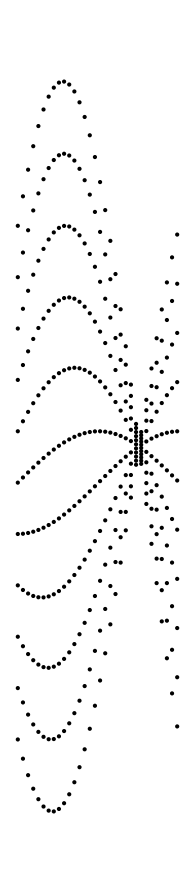

```mathematica
Graphics[Point[%]]
```

#### x

```mathematica
data=Join[Table[{x,-.45x+1},{x,-5,5,.1}],Table[{x,1.2x-1},{x,-5,5,.1}],Table[{x,-2x-2},{x,-5,5,.1}]];
```

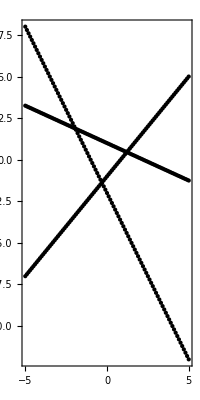

```mathematica
Graphics[Point[data],Frame->True,PlotRange->5]
```

```mathematica
data2=Flatten[Table[{m,#}&/@Apply[pNF[m,#1,#2]&,data,{1}],{m,0,Pi,0.01}],1];
```

```mathematica
bc=BinCounts[data2,{Range[0,π,.05]},{Range[-5,5,.05]}];
```

```mathematica
ListPlot3D[bc,PlotRange->All]
```

-Graphics3D-

```mathematica
?*`*Hough*
```